```mathematica
(* temp globals, to be localized in the Manipulate. *)
windowHalfWidth =3 ;
mMax = 30 ;
springLatticeData ={
{Darker@Orange,1,0,0,0,0,1},
{Darker@Green,0,1,0,0,1,0},
{Darker@Purple,1,1,0,0,0,0},
{Darker@Cyan,-1,1,1,0,1,0} ,
{Darker@Yellow,-1,1,1,0,1,0} 
} ;

springColorsByN = {
{1, 0} -> Darker@Orange,
{0, 1} -> Darker@Green,
{1, 1} -> Darker@Purple,
{1, -1} -> Darker@Cyan,
{-1, 0} -> Darker@Orange,
{0, -1} -> Darker@Green,
{-1, -1} -> Darker@Purple,
{-1, 1} -> Darker@Cyan,
{0, 0} -> Darker@Yellow
} ;

kMax = 0.9 ;
primaryDisplaySize = 200 ;
textDisOffset = {0.25, 0.25} ;




(* Based on a ListLinePlot version posted in: http://mathematica.stackexchange.com/a/37228/10 *)
ClearAll[springPoints] ;

springPoints::usage = "springPoints[ {point1, point2}, numberOfTurns, height, fractionToDrawAsLinesAtEnds ].  Example:

ListLinePlot[springPoints[{{1,2},{3,5}}], AspectRatio→Automatic, PlotStyle -> Darker[ Purple ] ]" ;

springPoints[ a12_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{a1, a2, n1, springDiff, nd, r, r1 },
{a1, a2} = a12 ;
n1 = Norm[a1] ;
springDiff = a2 - a1 ;
nd = Norm[springDiff] ;
r = RotationMatrix[ArcTan @@  springDiff ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
] ;

(*ClearAll[indexLabel] ;
indexLabel::usage = "k_i(or other character) in italic. indexLabel['k', 1]" ;
*)
indexLabel = Subscript[Style[#1,Italic], #2] & ;

(*ClearAll[kLable] ;
kLable::usage = "k_i(or other character) in italic and colored by spring index. kLable[k]" ;
*)
kLable = Style[ indexLabel["k", #], FontColor->First[springLatticeData[[#]]] ] & ;

massColors := ( Darker[{ Blue, Green, Purple, Red, Orange }][[Mod[#, 5] + 1] ] & );

massLabel := Style[indexLabel["m", #], massColors[#]] & ;

(*ClearAll[lineTable] ;*)
lineTable[ n_List, b_List, i_List ] :=Module[{first, second},
{first, second} = i ;
Table[
Line[
{-n[[first]]b[[first]] + j b[[second]],n[[first]]b[[first]] + j b[[second]]} 
] 
, {j, -n[[second]], n[[second]]}
]
] ;

(*ClearAll[ calcReciprocalBasis ] ;
calcReciprocalBasis::usage = "Return a reciprocal frame basis for a set of vectors.  This doesn't include the 2 π scaling that is common in solid state physics.  Example, displaying the desired Kronicker delta behaviour:

b = {{2,1},{-1/4, 2}} ;
g = calcReciprocalBasis[ b ] ;

{g[[1]].loc[[1]],
g[[1]].loc[[2]],
g[[2]].loc[[1]],
g[[2]].loc[[2]]}
" ;
*)
calcReciprocalBasis[loc_List] := Inverse[ Transpose[ loc ] ] ;

(*ClearAll[ pointsTable ] ;*)
pointsTable[ mPosFirstCell_List, latticeBasis_List, numberLatticeLinesToDisplay_List ] := Table[ 
mPosFirstCell + {i,j}. latticeBasis
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] ;

(*ClearAll[ projOp ] ;
projOp::usage = "given an input vector v⃗ = {v_x, v_y}, compute the projection matrix operator along the unit vector in that direction.

   projOp[{1, 0}] // MatrixForm = (1 | 0
0 | 0)
projOp[{0, 1}] // MatrixForm = (0 | 0
0 | 1)
projOp[{a,b}] // MatrixForm = (a^2/(a^2+b^2) | (a b)/(a^2+b^2)
(a b)/(a^2+b^2) | b^2/(a^2+b^2))
" ;*)
projOpU[v_List] := {{v[[1]]^2, v[[1]]v[[2]]},{v[[1]]v[[2]], v[[2]]^2}} ;
projOp[v_List] := projOpU[v]/(v. v) ;


(*ClearAll[ dynamicsMatrix ] ;
dynamicsMatrix::usage = "
The dynamics of the system are all contained in the matrix equation:

((ω^2 | 0
0 | ω^2)- dynamicsMatrix )ϵ⃗ = 0
 
where,

OverVector[u_n] = ϵ⃗ E^(I (OverVector[r_n] . q⃗ - ω t))
OverVector[r_n] = n_1 a⃗ + n_2b⃗ 

Examples:
Clear[d] 
d = dynamicsMatrix[{a_x,a_y}, {b_x,b_y}, k_1,k_2,k_3,k_4, m] ;
d[{q_x,q_y}] // MatrixForm // TraditionalForm 

Clear[d] 
d = dynamicsMatrix[ a{1, 0}, a{0, 1}, k_1,k_2,k_3,k_4, m] ;
d[{q_x,q_y}] // Factor  // MatrixForm // TraditionalForm

out: (*Cell[TextData[Cell[BoxData[
FormBox[
TagBox[
RowBox[{"(", "", GridBox[{
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "1"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "2"], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"]},
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "2"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "2"], ")"}]}]}], ")"}]}], "m"]}
},
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {
Offset[0.27999999999999997`], {
Offset[0.7]}, 
Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {
Offset[0.2], {
Offset[0.4]}, 
Offset[0.2]}, "RowsIndexed" -> {}}], "", ")"}],
Function[BoxForm`e$, 
MatrixForm[BoxForm`e$]]], TraditionalForm]],
CellChangeTimes->{3.5990563268386803`*^9, {3.5990565758059196`*^9, 3.5990566126100254`*^9}, 3.599056660298753*^9, {3.599056905058752*^9, 3.599056911414116*^9}, 3.5990570494260097`*^9, 3.5990570802537727`*^9, {3.5990923676281567`*^9, 3.599092423296341*^9}}]]])

" ;*)
dynamicsMatrix[ a_List, b_List, kk1_, kk2_, kk3_, kk4_, mm_ ] := (4/mm)(
projOp[a]kk1 Sin[ a . # /2 ]^2 + projOp[b]kk2 Sin[ b . # /2 ]^2+ projOp[a + b]kk3 Sin[ (b + a) . # /2 ]^2+ projOp[b - a] kk4 Sin[ (b  -a) . # /2 ]^2) & ;

(*ClearAll[ frequencyPlot ] ;
frequencyPlot::usage = "frequencyPlot[ dynamicsMatrix[{1,0}, {0,1}, 8, { 2 Pi, 2 Pi }, 0.5, 0.5, 0.25, 0.25, 1][#] &, ld ]" ;*)
frequencyPlot[mat_, ld_, meshSz_] := Module[{eigTable, qMax, omegaPointList, range},

qMax = 2 Pi("reciprocalNorms" /. ld) ;

eigTable = Flatten[Re[Table[  {{qx, qy} ,Eigenvalues[ mat[ {qx, qy}  ] // N ]}, {qx, -qMax[[1]]/2, qMax[[1]]/2, qMax[[1]]/ meshSz}, {qy, -qMax[[2]]/2, qMax[[2]]/2, qMax[[2]]/ meshSz} ] ],1] ;

omegaPointList[nn_] := Flatten[{#[[1]],Sqrt[#[[2]]][[nn]]}]&/@ eigTable  ;

range = (Dimensions[mat[ {0,0}  ]] // First // Range) ;

ListPlot3D[ omegaPointList[#] &/@ range (*Table[{#[[1]][[1]], #[[1]][[2]], Sqrt[#[[2]][[j]]]} &/@ eigTable, {j, Range[2]}]*), PlotRange -> Full , ImageSize->primaryDisplaySize,(*ImagePadding->30,*) AxesLabel->{"q_x", "q_y"}]
] ;

(*ClearAll[ calcDynamics ] ;*)
calcDynamics[calcResults_List, dynmatrix_,ql_List] := Module[{reciprocalNorms, q, eigensystem},

{reciprocalNorms}={"reciprocalNorms"} /. calcResults ;

q=(2 Pi ql[[#]]reciprocalNorms[[#]] &/@ Range[2]) ;

eigensystem = ({Sqrt[#[[1]]], #[[2]]}&/@(Eigensystem[ dynmatrix[q] ] // Transpose)) ;

{q, eigensystem}
] ;

(*ClearAll[ showDynamics ] ;*)
showDynamics[calcResults_List, {q_, eigensystem_}, oi_Integer, scaleVar_, a_, b_ ] :=Module[{pointsDataTable,numberLatticeLinesToDisplay, e, omega, points, lines, nu},

{pointsDataTable,numberLatticeLinesToDisplay, lines}={"pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

{omega, e} = eigensystem[[oi]] ;

points = pointsDataTable + Table[ 
 scaleVar Re[e E^(I( q . (a i + b j) - omega #)) ]
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] & ;

nu = 2 Pi If[ omega == 0, 1, 1/omega] ; 

(Show[{
ListPlot[ points[nu #]
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
, PlotStyle->Directive[PointSize[Large]]
], 
Graphics[{
lines
}]
}] &)
] ;
```

```mathematica
(*Manipulate[tick;
Dynamic@If[ tabNumber == dynTab,
dynPlot[tau],
If[tabNumber == freqTab,
frequencyPlot[ matrix, locDependentCalc, meshSize ],
plotSprings[springPlotH,springPlotNE,springPlotNW,springPlotV, locDependentCalc]  ] ]
,
TabView[{
"dynamics" ->  Column[
tabNumber = dynTab ;
{ 
Row[ {OverVector["q"], ", normalized to unit square:"}],
Row[{
(* q here in normalized coordinates, because of an order of operations issue.  This Grid appears to be evaluated before the Init section?  Not sure how to fix.  Would have to deal with that to allow one vs. two atom basis too (for the omegaIndex SetterBar). *)
Slider2D[Dynamic[qLoc,(
qLoc=#;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&], {{-1/2,-1/2}, {1/2,1/2}},
ContinuousAction->False], " ",  Dynamic[(NumberForm[qLoc, 5] // MatrixForm)]
}],
Row[{"Time, normalized to one period:"}],
Row[{Manipulator[Dynamic[tau,(tau=#;tick=Not[tick])&],{0,1},ImageSize->Tiny,ContinuousAction->True]}
, ImageSize->{200,60}],
Text["Angular frequency ω(q), selection:"],
SetterBar[Dynamic[omegaIndex,(
omegaIndex=#;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&], Dynamic@Range[2 nAtoms] ]

}]
, "ω(q⃗)" ->  Row[ tabNumber = freqTab ;{ "Mesh size ",
(* FIXME: Want to be able to select a plane here, 
   displaying both a plane plot and the 3D plot (or a checkbox for one or the other).*)
Manipulator[Dynamic[meshSize,(meshSize=#;tick=Not[tick])&],{2,20,2},ImageSize->Tiny,ContinuousAction->False]," ", Dynamic[meshSize] 
}]
, "parameters"->Column[ tabNumber = parametersTab ;{
Text[ "Spring constants:" ],
Grid[{
{
Row[{ "Horizontal: ",kLable[1], " || ", OverVector["a"]," "}],
Row[{
Manipulator[
Dynamic[k1,(
k1=#;
springPlotH = springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; 
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
,
" ",Dynamic[NumberForm[k1,3]]
}]
},
{
Row[{ "Vertical: ",kLable[2], " || ", OverVector["b"]," "}],
Row[{Manipulator[
Dynamic[k2,(
k2=#;
springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k2,3]]
}] 
},
{
Row[{ "Diagonal: ",kLable[3], " || (",  OverVector["b"], " + ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k3,(
k3=#;
springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k3,3]]
}]
},
{
Row[{ "Diagonal: ",kLable[4], " || (",  OverVector["b"], " - ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k4,(
k4=#;
springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k4,3]]
}]
}
}], 
LocatorPane[
Dynamic[{aLoc, bLoc, mLoc1, mLoc2},
({aLoc, bLoc, mLoc1, mLoc2}=#; 
(* Lance, testing for me, managed to break the physical constants tab, by moving the points too close to the origin *)
aLoc = If[ aLoc. aLoc < lanceTestForceField, aLocDefault, aLoc ] ;
bLoc = If[ bLoc. bLoc < lanceTestForceField, bLocDefault, bLoc ] ;
locDependentCalc = locDependent[ aLoc, bLoc, mLoc1 ] ;
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,Dynamic@Graphics[ {
Arrow[{{0,0}, aLoc}]
,Arrow[{{0,0}, bLoc}]
,Text[OverVector["a"],aLoc/2 + {0.5, 0.5}]
,Text[OverVector["b"],bLoc/2 + {0.5, 0.5}]
,Text[indexLabel["m", 1],mLoc1 + {0.5, 0.5}]
,Text[indexLabel["m", 2],mLoc1 + {0.5, 0.5}]
},PlotRange->{{-windowHalfWidth,windowHalfWidth},{-windowHalfWidth,windowHalfWidth}}]
,LocatorAutoCreate->True
,ContinuousAction->False
]
} ]
}, Dynamic @tabNumber ] 

,{{tick,False},None}
,{{nAtoms, 2}, None}
,{{k1,0.5},None}
,{{k2,0.5},None}
,{{k3,0.25},None}
,{{k4,0.25},None}
,{{m1, 10}, None}
,{{m2, 10}, None}
,{{aLoc,{2,1}}, None}
,{{bLoc,{-1/4,2}}, None}
,{{aLocDefault,{2,1}}, None}
,{{bLocDefault,{-1/4,2}}, None}
,{{mLoc1,{1,2}}, None}
, {{lanceTestForceField, 0.1}, None}

,{{qLoc,{0.1,-0.1}},None}
,{{tau,0},None}
,{{omegaIndex, 1}, None}
,{{dynamics, {}}, None}
,{{scale, 0.1}, None}
,{{dynPlot, {}}, None}

,{{meshSize,8},None}
,{{tabNumber,1},None}
,{{locDependentCalc, {} }, None}


,{{springPlotH,{}},None}
,{{springPlotNE,{}},None}
,{{springPlotNW,{}},None}
,{{springPlotV,{}},None}
,{{matrix, {}}, None}

(*generic globals *)
,{{windowHalfWidth, 3}, None}
,{{springLatticeData,{
{Darker@Orange,1,0,0,0,0,1},
{Darker@Green,0,1,0,0,1,0},
{Darker@Purple,1,1,0,0,0,0},
{Darker@Cyan,-1,1,1,0,1,0} }
 } , None}
,{{kMax, 0.9}, None}
,{{primaryDisplaySize, 200}, None}

,{{mMax, 30}, None}
,{{dynTab, 1}, None}
,{{freqTab, 2}, None}
,{{parametersTab, 3}, None}

,TrackedSymbols:>{tick}
,ControlPlacement->Left
,SaveDefinitions->True
,SynchronousInitialization->False
, Initialization:> { 


locDependentCalc = locDependent[ aLoc, bLoc, mLoc1 ] ; 
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;

}
]*)
```

```mathematica
(*ClearAll[ locDependent ] ;
locDependent::usage = "Locator dependent calculations (i.e. based on the mass positions and the unit cell basis vectors)

Example:

locDependent[{1/2,1}, {1,1/2}, {{0.1,0.2} + {1/2,1} + {1,1/2}, {0.3, 0.5} - {1/2,1} - {1,1/2}}]

Will see: {0.1,0.2}, {0.3, 0.5} ; as the mPosFirstCell values.
" ;*)
locDependent[a_, b_, m_List] := Module[{numMasses,latticeBasis, numberLatticeLinesToDisplay,reciprocalBasis,mObliqueComponents, mPosFirstCell},
latticeBasis = {a, b} ;
numberLatticeLinesToDisplay = (Ceiling[  Abs[windowHalfWidth/ latticeBasis[[#]][[#]]]] & /@ Range[2]) ;
reciprocalBasis = calcReciprocalBasis[ latticeBasis ] ;

numMasses = Dimensions[m] // First ;
mObliqueComponents = Table[m[[ i ]] . reciprocalBasis[[ j ]], {i, numMasses}, {j, 2}] ;
mPosFirstCell = (m[[#]] - Floor[mObliqueComponents[[#]]] . latticeBasis ) & /@ Range[numMasses] ;

{
"aLoc"->a,"bLoc"->b,"mLoc"->m,
"numMasses" -> numMasses,
"latticeBasis"->latticeBasis,
"latticeNorms"->(Norm[latticeBasis[[#]]] & /@ Range[2]),
"latticeUnitVectors"->(Normalize[latticeBasis[[#]]] & /@ Range[2]),
"numberLatticeLinesToDisplay"-> numberLatticeLinesToDisplay,
"reciprocalBasis"-> reciprocalBasis,
"reciprocalNorms"-> (Norm[reciprocalBasis[[#]]] & /@ Range[2]),
"mObliqueComponents"-> mObliqueComponents,
"mPosFirstCell"-> mPosFirstCell,
"pointsDataTable"-> ((pointsTable[mPosFirstCell[[#]],latticeBasis,numberLatticeLinesToDisplay]) &/@ Range[numMasses]),
"lineTable" -> (lineTable[ numberLatticeLinesToDisplay, latticeBasis, # ] & /@ Permutations[{1,2}])
}
] ;




(*ClearAll[ plotSprings ] ;
plotSprings::usage = "Example:

Module[{ld},
ld = locDependent[{1/2,1}, {1,1/2}, {{0.1,1.2} + {1/2,1} + {1,1/2}, {1.3, 0.5} - {1/2,1} - {1,1/2}}] ;
plotSprings[{10,20}, ld ] 
]
" ;*)
plotSprings[massValue_List, calcResults_] := Module[{aLoc, bLoc,mLoc,numMasses,pointsList,latticeBasis,reciprocalBasis,pointsDataTable, numberLatticeLinesToDisplay, lines},

{aLoc, bLoc,mLoc,numMasses,latticeBasis,reciprocalBasis,pointsDataTable,numberLatticeLinesToDisplay, lines}={"aLoc", "bLoc","mLoc","numMasses","latticeBasis","reciprocalBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable"}  /. calcResults  ;

pointsList[n_Integer] :={massColors[n],
,PointSize[Sqrt[massValue[[n]]/mMax/500]]
,Point[ # ] & /@ pointsDataTable[[n]]
,Text[massLabel[ n],mLoc[[n]] + textDisOffset]
} ;

(*Show[{*)
Graphics[
Flatten[{
{
lines
,Blue,Arrow[{{0,0}, reciprocalBasis[[#]]}] & /@ Range[2]
,Thick,Arrowheads[0.05]
,Red,Arrow[{{0,0}, latticeBasis[[#]]}] & /@ Range[2]
,Text[OverVector["a"],aLoc/2 + textDisOffset]
,Text[OverVector["b"],bLoc/2 + textDisOffset]
},
pointsList[#] &/@ Range[numMasses]
}]
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
](*,
kp1,
kp2,
kp3,
kp4*)
(*}]*)
] ;


(*TODO:
20. mass sizes are scaling with order of addition, and not the mass scalar values.
  4. spring plots based on nn: kArray -> geometry array (loc dependent) + sort/select up to nn-count.
>> count all origin cell couplings.  Then count nn couplings for each mass up to num-interactions (change selector)
21. need a Lance-force-field for the mass separation too.
17. generate the interaction data.
6. generate the matrix
16. re-introduce the tab, initially with just the constants selector tab, and get the presentation looking right now that I have the LocatorPane and the Graphic combined.

18. generate the dynamics data.
19. generate the frequency data.
12. re-introduce the rest of the tabs, and work through n-mass dependencies in the rest of that code.
9. move all the functions back into the Initializer section.
10. move the global values back into Manipulate locals (9 first).
11. re-enable Sync init and Save def.

Nice to haves:
13. remove all but the colors from springLatticeData, and rename.
15. a message box on user error: 
  - when an angle or distance from origin change has driven a reset of the lattice vectors.
- when too many of the locators have been deleted and everything is reset. 
*)
Manipulate[
tick;
Grid[{
{"Number of interactions: ", 
Row[{
"  ",
Manipulator[
Dynamic[nn,(
nn=#;
tick=Not[tick])&],
 {1, Dynamic[-1 +10 lastNumMasses ], 1} ,
ImageSize->Tiny,
ContinuousAction->False
], 
" ",
Dynamic@nn
}]
},
{
Row[{
"mass: ", 
If [ lastNumMasses > 1,
SetterBar[
Dynamic[m1Sel,(
m1Sel=#;
massValue = mScalarArray[[m1Sel]];
tick=Not[tick])&], 
(# -> massLabel[ # ]&/@ Range[lastNumMasses])
],
massLabel[ 1]
],
" ",
Manipulator[
Dynamic[massValue,(
massValue = # ;
mScalarArray[[m1Sel]]=massValue ;
tick=Not[tick])&]
,{0.25,Dynamic@mMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[mScalarArray[[m1Sel]],3]]
}]
},
{
"coupling from origin to neighbouring: " , 
If [ lastNumMasses > 1,
SetterBar[
Dynamic[m2Sel,(
m2Sel=#;
tick=Not[tick])&], 
(# -> massLabel[ #] &/@ Range[lastNumMasses])
],massLabel[ 1]
]
},
{
Row[{ "horizontal: ",kLable[1], " || ", OverVector["a"]," "}],
Row[{
Manipulator[
Dynamic[k1,(
k1=#;
kArray = alterKArrayElements[ 1, k1 ] ;

tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
,
" ",Dynamic[NumberForm[k1(*kArraySelect[1]*),3]]
}]
},
{
Row[{ "vertical: ",kLable[2], " || ", OverVector["b"]," "}],
Row[{Manipulator[
Dynamic[k2,(
k2=#;
kArray = alterKArrayElements[ 2, k2 ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k2(*kArraySelect[2]*),3]]
}] 
},
{
Row[{ "diagonal: ",kLable[3], " || (",  OverVector["b"], " + ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k3,(
k3=#;
kArray = alterKArrayElements[ 3, k3 ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k3(*kArraySelect[3]*),3]]
}]
},
{
Row[{ "diagonal: ",kLable[4], " || (",  OverVector["b"], " - ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k4,(
k4=#;
kArray = alterKArrayElements[ 4, k4 ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k4(*kArraySelect[4]*),3]]
}]
},
If [ lastNumMasses > 1,
{ 
Row[{ 
"origin cell coupling from ", massLabel[ m1Sel]," to ",
If [ lastNumMasses > 2,
SetterBar[
Dynamic[moSel,(
moSel=#;
tick=Not[tick])&], 
(# -> massLabel[ #] &/@ (DeleteCases[Range[lastNumMasses],m1Sel]))
],
massLabel[ 2]
]
, " ", kLable[5], ": "
}],
Row[{Manipulator[
Dynamic[k5,(
k5=#;
(*{1,2,{0,0}}*)
kArray = alterKarrayOriginElement[ k5 ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[ k5 (*kArrayOriginSelect*),3]]
}]
},
{} (* else: dummy *)
],
(*For Debugging:*)
(*{ "m1Sel, m2Sel, moSel = ", {m1Sel, m2Sel, moSel}},*)
(*{ "mScalarArray = ", mScalarArray },*)
(*{"u = ", u},*)
(*{"kArray = ", kArray},*)
(*{"k1, k2, k3, k4, k5 = ", {k1, k2, k3, k4, k5}},*)
{
LocatorPane[ Dynamic[u,(
u = If [ (Dimensions[#] // First)<3, Flatten[ {locDefault, {mLocDefault}}, 1], #] ;

(* This assumes just one added at a time, but that's probably okay.  Only Alt-click delete of more than one at once appears possible, since it doesn't refresh after Alt-click for delete until some other locator is adjusted. *)
{mScalarArray,kArray} =If [ nMasses[u] > lastNumMasses, 
{
Append[mScalarArray, defaultMass], 
growKarray[nMasses[u]]
}, 
{
Take[mScalarArray, nMasses[u] ], 
Select[kArray, Max[{#[[1]], #[[2]]}] ≤  nMasses[u]&]
}] ; 

(* Don't allow the lattice vector end points to be too close to the origin *)
u[[1]] = If[ u[[1]]. u[[1]] < minSquaredDistanceFromOrigin, locDefault[[1]], u[[1]] ] ;
u[[2]] = If[ u[[2]]. u[[2]] < minSquaredDistanceFromOrigin, locDefault[[2]], u[[2]] ] ;

(* Don't allow the angle between lattice vectors get too small *)
{u[[1]], u[[2]]} = resetLatticeVectorsIfAngleTooSmall[ minAngleBetweenLatticeVectors ] ;

lastNumMasses = nMasses[u] ;

(*These are in case the number of locators were changed and we have a mass selected that is invalid.*)
m1Sel = If [ m1Sel >lastNumMasses, 1, m1Sel] ;
m2Sel = If [ m2Sel >lastNumMasses, 1, m2Sel] ;
moSel = If [ moSel >lastNumMasses, 1, moSel ] ;
moSel = If [ lastNumMasses > 2,
If [moSel == m1Sel, 
First[DeleteCases[Range[lastNumMasses],m1Sel]], 
moSel], 
1] ;

ld = locDependent[u[[1]], u[[2]], Drop[u,2]] ;
tick=Not[tick])&],
(* Why doesn't Alt-click to remove existing Locator refresh this plot?  Workaround: move one of the other locators to refresh *)
plotSprings[ 10# &/@ Range[lastNumMasses], ld ],
LocatorAutoCreate->True, 
ContinuousAction->False
]
}
}
]
,{{tick,False},None}

, {{minSquaredDistanceFromOrigin, 0.1}, None}
, {{minAngleBetweenLatticeVectors, Pi/6}, None}
,{{locDefault,{{0.5, 1.3}, {2.3, 0.9}}}, None}
, {{mLocDefault, {0.9,0.7}}, None}
,{{u,{
{0.5, 1.3}, {2.3, 0.9},
{0.9,0.7}(*,
{0.9,1.6},
{1.8,1.9}*)
}},None}
, {{nn, 1},None}
, {{lastNumMasses, 1}, None}
,{{ld, {}}, None}

,{{m1Sel, 1}, None}
,{{m2Sel, 1}, None}
,{{moSel, 1}, None}
,{{k1,0.5},None}
,{{k2,0.5},None}
,{{k3,0.25},None}
,{{k4,0.25},None}
,{{k5,0.25},None}
,{{defaultMass, 10}, None}
,{{mScalarArray, {10}}, None}
, {{kArray, {}}, None} 
,{{kDefaults, {0.5, 0.5, 0.25, 0.25, 0.25}}, None}

,{{kMax, 0.9}, None}
,{{mMax, 30}, None}
,{{nArray, {{1,0},{0, 1}, {1,1}, {1,-1}} }, None}


,TrackedSymbols:>{tick}
,ControlPlacement->Left
(*,SaveDefinitions->True
,SynchronousInitialization->False
*)
, Initialization :> {
nMasses := ((Dimensions[#] // First) -2) & ;

constructKArrayElements[ i_Integer, j_Integer  ] := Module[{a},
a = Flatten[Table[{i, j, s nArray[[n]]} -> kDefaults[[n]], {s, -1, 1, 2}, {n, 4} ], 1] ;

If [ i < j, Append[a,{i,j,{0,0}} -> kDefaults[[5]]], a ] 
] ;

constructKArray[ r_Integer ] := Flatten[Table[constructKArrayElements[i,j], {i, r}, {j,r}], 2] ;

alterKArrayElements[ ni_Integer, v_ ] := (kArray /. {
Rule[{m1Sel,m2Sel, nArray[[ni]]}, _] :> Rule[{m1Sel,m2Sel, nArray[[ni]]}, v],
Rule[{m1Sel,m2Sel, -nArray[[ni]]}, _] :> Rule[{m1Sel,m2Sel, -nArray[[ni]]}, v]
} ) ;

alterKarrayOriginElement[v_] :=Module[{m1oSet},
m1oSet = Append[Sort[{m1Sel, moSel}], {0,0}] ;

kArray /. Rule[m1oSet, _] :> Rule[m1oSet, v]
] ;

(* UnitTest for alter* : *)
(*kArraySelect[ ni_Integer ] := ({m1Sel,m2Sel,nArray[[ni]] } /. kArray) ;
kArrayOriginSelect := (Append[Sort[{m1Sel, moSel}], {0,0}]  /. kArray) ;
*)

growKarray[ nmNew_Integer ] := Module[{k2},
k2 = Flatten[
(constructKArrayElements[#[[1]],#[[2]]] &)/@ (Select[Flatten[Table[ {i,j}, {i, nmNew}, {j, nmNew}], 1], Max[#] == nmNew &]), 2] ;

Flatten[{kArray, k2}, 1]
] ;

resetLatticeVectorsIfAngleTooSmall[minAngle_] := Module[{t},
t = Abs[ArcCos[Normalize[u[[1]]] . Normalize[u[[2]]]]] ;
t = If [ t > Pi/2, Pi-t, t] ;

If[ t < minAngle,
locDefault, {u[[1]], u[[2]]}]
] ;

ld = locDependent[u[[1]], u[[2]], Drop[u,2]] ;
kArray = constructKArray[ 1 ] ;

}
]
```

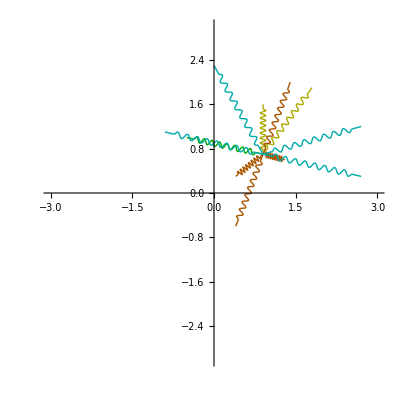

```mathematica
(*Module[{kArray, k2, kDefaults},
kDefaults = Range[5] ;
kArray = constructKArray[ 3, kDefaults ] ;
k2 = constructKArray[ 4, kDefaults ] ;
(*kArray = Flatten[Table[constructKArray[i,j, kDefaults], {i, 3}, {j,3}], 2] ;
k2 = Flatten[Table[constructKArray[i,j, kDefaults], {i, 4}, {j,4}], 2] ;*)

(*query*)
(*{1,1,{1,0 } } /. kArray *)

(*update*)

kArray = (kArray /. {Rule[{1,1, {1,0}}, _] :> Rule[{1,1, {1, 0}}, 7],Rule[{1,1, {0,1}}, _] :> Rule[{1,1, {0, 1}}, 7]} )  ;
(*DeleteCases[(k2 /. kArray), Rule[_Real,_Real] ]*)
kArray

(*prune*)
(*DeleteCases[kArray, Rule[{_,2, _},_] | Rule[{2,_, _},_] ]*)

(*(#[[1]] -> #[[2]])&/@ DeleteCases[ (kArray /. Rule -> List), {{1,1, _}, _}]*)
(*kArray*)
]*)

(*Module[{k},
k = {{1,1} -> a, {2,3} -> b} ;
k /. Rule[{1,1}, _] :> Rule[{1,1}, c] 
]*)

(*Manipulate[
constructKArray[ 2, Range[5] ]
,{{nArray, {{1,0},{0, 1}, {1,1}, {1,-1}} }, None}
, Initialization:> {
constructKArrayElements[ i_Integer, j_Integer, kD_List ] := Module[{a},
a = Flatten[Table[{i, j, s nArray[[n]]} -> kD[[n]], {s, -1, 1, 2}, {n, 4} ], 1] ;

If [ i < j, Append[a,{i,j,{0,0}} -> kD[[5]]], a ] 
] ;

constructKArray[ r_Integer, kD_List ] := Flatten[Table[cconstructKArrayElements[i,j, kDefaults], {i, r}, {j,r}], 2] ;
}]*)


(*ClearAll[ springLatticePlot ] ;*)
(*springLatticePlot[ calcResults_List, {color_, iOff_Integer, jOff_Integer, iStartAdj_, jStartAdj_, iRangeAdj_Integer, jRangeAdj_Integer},springStrengthFraction_] := Module[{pt, pointsDataTable, numberLatticeLinesToDisplay},

{pt,numberLatticeLinesToDisplay}={"pointsDataTable","numberLatticeLinesToDisplay"} /. calcResults ;
(*pointsDataTable = pt[[1]] ; (*FIXME*)*)

ListLinePlot[
Flatten[Table[
springPoints[ pointsDataTable[[i,j]], pointsDataTable[[i+iOff,j + jOff]], Ceiling[8 springStrengthFraction] ],
{i, 1 + iStartAdj, numberLatticeLinesToDisplay[[1]] * 2 + iRangeAdj},
{j, 1 + jStartAdj, numberLatticeLinesToDisplay[[2]] * 2 + jRangeAdj}
], 2] ,
PlotStyle ->  color ]
];*)

ClearAll[ selectCouplings ] ;
(*selectCouplings := Module[{m1Sel, m2Sel,moSel, kArray, m1oSet, nMasses, k1, k2},
m1Sel =2 ;
m2Sel = 1 ;
nMasses = 3 ;
m1oSet = Append[Sort[{m1Sel, m2Sel}], {0,0}] ;
kArray = {(*{1,2,{0,0}}->0.25,{2,3,{0,0}}->0.25,{1,3,{0,0}}->0.25,*){1,1,{-1,0}}->0.5,{1,1,{0,-1}}->0.5,{1,1,{-1,-1}}->0.25,{1,1,{-1,1}}->0.25,{1,1,{1,0}}->0.5,{1,1,{0,1}}->0.5,{1,1,{1,1}}->0.25,{1,1,{1,-1}}->0.25,{1,2,{-1,0}}->0.5,{1,2,{0,-1}}->0.5,{1,2,{-1,-1}}->0.25,{1,2,{-1,1}}->0.25,{1,2,{1,0}}->0.5,{1,2,{0,1}}->0.5,{1,2,{1,1}}->0.25,{1,2,{1,-1}}->0.25,{1,2,{0,0}}->0.25,{2,1,{-1,0}}->0.5,{2,1,{0,-1}}->0.5,{2,1,{-1,-1}}->0.25,{2,1,{-1,1}}->0.25,{2,1,{1,0}}->0.5,{2,1,{0,1}}->0.5,{2,1,{1,1}}->0.25,{2,1,{1,-1}}->0.25,{2,2,{-1,0}}->0.5,{2,2,{0,-1}}->0.5,{2,2,{-1,-1}}->0.25,{2,2,{-1,1}}->0.25,{2,2,{1,0}}->0.5,{2,2,{0,1}}->0.5,{2,2,{1,1}}->0.25,{2,2,{1,-1}}->0.25,{1,3,{-1,0}}->0.5,{1,3,{0,-1}}->0.5,{1,3,{-1,-1}}->0.25,{1,3,{-1,1}}->0.25,{1,3,{1,0}}->0.5,{1,3,{0,1}}->0.5,{1,3,{1,1}}->0.25,{1,3,{1,-1}}->0.25,{1,3,{0,0}}->0.25,{2,3,{-1,0}}->0.5,{2,3,{0,-1}}->0.5,{2,3,{-1,-1}}->0.25,{2,3,{-1,1}}->0.25,{2,3,{1,0}}->0.5,{2,3,{0,1}}->0.5,{2,3,{1,1}}->0.25,{2,3,{1,-1}}->0.25,{2,3,{0,0}}->0.25,{3,1,{-1,0}}->0.5,{3,1,{0,-1}}->0.5,{3,1,{-1,-1}}->0.25,{3,1,{-1,1}}->0.25,{3,1,{1,0}}->0.5,{3,1,{0,1}}->0.5,{3,1,{1,1}}->0.25,{3,1,{1,-1}}->0.25,{3,2,{-1,0}}->0.5,{3,2,{0,-1}}->0.5,{3,2,{-1,-1}}->0.25,{3,2,{-1,1}}->0.25,{3,2,{1,0}}->0.5,{3,2,{0,1}}->0.5,{3,2,{1,1}}->0.25,{3,2,{1,-1}}->0.25,{3,3,{-1,0}}->0.5,{3,3,{0,-1}}->0.5,{3,3,{-1,-1}}->0.25,{3,3,{-1,1}}->0.25,{3,3,{1,0}}->0.5,{3,3,{0,1}}->0.5,{3,3,{1,1}}->0.25,{3,3,{1,-1}}->0.25} ;

k1 = Select[ (kArray /. Rule -> List),(#[[1]][[1]] == m1Sel) && (#[[1]][[3]] ≠ {0, 0}) &]  ;
(*If [ nMasses > 1, Append[k1, 
Flatten[Select[ (kArray /. Rule -> List),#[[1]] == {m1oSet[[1]], m1oSet[[2]], {0,0}} & ], 1]
], k1 ]*)
k1
]*)

ClearAll[ relDifferences ] ;
relDifferences[ r_List,mp_List, ke_List ] := Module[{d, pOrigin, pOther},
pOrigin = mp[[ First[ke][[1]] ]] ;
pOther = mp[[ First[ke][[2]] ]]+ First[ke][[3]] . r  ;
d = pOther - pOrigin ;
dn = d .d ;

{
dn, (*d,*) pOrigin, pOther,(projOpU[d]/dn  (*// MatrixForm*))
}
] ;

ClearAll[ calcCouplings ] ;
(*calcCouplings::usage = "Returns a pair of sets for each origin m_i coupling:
First has all the origin cell couplings for that mass.
Second has all the nn couplings for each mass sorted by distance from mass.  Can use that to select up to num-interactions." ;*)
calcCouplings[kA_List, u_List] := Module[{r, mp, t, t1, t2, nm},

r = Take[u, 2] ;
mp = Drop[u, 2] ;
nm = Dimensions[mp] // First ;

t = Append[#, relDifferences[r, mp, #] ]&/@ kA ;
t = Flatten[{#[[1]], {#[[2]]}, #[[3]]}, 1] &/@ t ;

t1 = Table[
Sort[(Select[ t, (#[[1]] == i) && (#[[3]] ≠ {0, 0}) &]), #1[[5]] < #2[[5]] &]
, {i, nm}
] ;

t2 = Select[ t,#[[3]] == {0, 0} &] ;
(* the rest of the permutations: *)
t2 = Flatten[{t2, Flatten[{{#[[2]], #[[1]]}, Drop[#, 2]}, 1] &/@ t2}, 1]  ;
t2 = Table[
Sort[(Select[ t2, (#[[1]] == i) &]), #1[[5]] < #2[[5]] &]
, {i, nm}
] ;

{t2, t1}
]

Module[{kA, u, cOrigin, cRest, x, t1, t2, p, n, originSprings, nSprings},

kA = {{1,1,{-1,0}}->0.5,{1,1,{0,-1}}->0.5,{1,1,{-1,-1}}->0.25,{1,1,{-1,1}}->0.25,{1,1,{1,0}}->0.5,{1,1,{0,1}}->0.5,{1,1,{1,1}}->0.25,{1,1,{1,-1}}->0.25,{1,2,{-1,0}}->0.5,{1,2,{0,-1}}->0.5,{1,2,{-1,-1}}->0.25,{1,2,{-1,1}}->0.25,{1,2,{1,0}}->0.5,{1,2,{0,1}}->0.5,{1,2,{1,1}}->0.25,{1,2,{1,-1}}->0.25,{1,2,{0,0}}->0.25,{2,1,{-1,0}}->0.5,{2,1,{0,-1}}->0.5,{2,1,{-1,-1}}->0.25,{2,1,{-1,1}}->0.25,{2,1,{1,0}}->0.5,{2,1,{0,1}}->0.5,{2,1,{1,1}}->0.25,{2,1,{1,-1}}->0.25,{2,2,{-1,0}}->0.5,{2,2,{0,-1}}->0.5,{2,2,{-1,-1}}->0.25,{2,2,{-1,1}}->0.25,{2,2,{1,0}}->0.5,{2,2,{0,1}}->0.5,{2,2,{1,1}}->0.25,{2,2,{1,-1}}->0.25,{1,3,{-1,0}}->0.5,{1,3,{0,-1}}->0.5,{1,3,{-1,-1}}->0.25,{1,3,{-1,1}}->0.25,{1,3,{1,0}}->0.5,{1,3,{0,1}}->0.5,{1,3,{1,1}}->0.25,{1,3,{1,-1}}->0.25,{1,3,{0,0}}->0.25,{2,3,{-1,0}}->0.5,{2,3,{0,-1}}->0.5,{2,3,{-1,-1}}->0.25,{2,3,{-1,1}}->0.25,{2,3,{1,0}}->0.5,{2,3,{0,1}}->0.5,{2,3,{1,1}}->0.25,{2,3,{1,-1}}->0.25,{2,3,{0,0}}->0.25,{3,1,{-1,0}}->0.5,{3,1,{0,-1}}->0.5,{3,1,{-1,-1}}->0.25,{3,1,{-1,1}}->0.25,{3,1,{1,0}}->0.5,{3,1,{0,1}}->0.5,{3,1,{1,1}}->0.25,{3,1,{1,-1}}->0.25,{3,2,{-1,0}}->0.5,{3,2,{0,-1}}->0.5,{3,2,{-1,-1}}->0.25,{3,2,{-1,1}}->0.25,{3,2,{1,0}}->0.5,{3,2,{0,1}}->0.5,{3,2,{1,1}}->0.25,{3,2,{1,-1}}->0.25,{3,3,{-1,0}}->0.5,{3,3,{0,-1}}->0.5,{3,3,{-1,-1}}->0.25,{3,3,{-1,1}}->0.25,{3,3,{1,0}}->0.5,{3,3,{0,1}}->0.5,{3,3,{1,1}}->0.25,{3,3,{1,-1}}->0.25} /. Rule -> List ;

u = {
{0.5, 1.3}, {2.3, 0.9},
{0.9,0.7},
{0.9,1.6},
{1.8,1.9}
} ;
(*{
{Subscript[a, 1], Subscript[a, 2]}, {Subscript[b, 1], Subscript[b, 2]},
{Subscript[m, 11],Subscript[m, 12]},
{Subscript[m, 21],Subscript[m, 22]},
{Subscript[m, 31],Subscript[m, 32]}
} ; *)

{t2, t1} = calcCouplings[kA, u] ;

originSprings = ListLinePlot[
springPoints[ Take[#, {6,7}] ] ,
AspectRatio->Automatic, 
PlotRange -> {{-3, 3}, {-3,3}},
PlotStyle -> (#[[3]] /. springColorsByN) ] &/@ t2[[1]]  ;

n = 9 ;

nSprings = ListLinePlot[
springPoints[ Take[#, {6,7}] ] ,
AspectRatio->Automatic, 
PlotStyle -> (#[[3]] /. springColorsByN) ] &/@ Take[t1[[1]], n]  ;

Show[ Flatten[{originSprings, nSprings}, 1 ] ]
(*Dimensions[ t1[[1]] ]*)

(*ListLinePlot[
Flatten[springPoints[ Take[#, {6,7}] ] &/@ t2, 1],
AspectRatio->Automatic, 
PlotStyle -> Darker[ Purple ] ]*)

(* t1[[1]]*)
(*{t2, t1}*)
]
```

```mathematica
(*Style[indexLabel["m", 1], massColors[1]]*)
```

```mathematica
(*ListLinePlot[springPoints[{{0.9,0.7},{0.9,1.6}}], AspectRatio->Automatic, PlotStyle -> Darker[ Purple ] ]*)
```